```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
inputfile=OpenRead["phi.txt"]
```

InputStream[…]

```mathematica
data=ReadList[inputfile,{Number,Number,Number}];
```

```mathematica
Close[inputfile]
```

phi.txt

```mathematica
ndata=Length[data]
```

1000

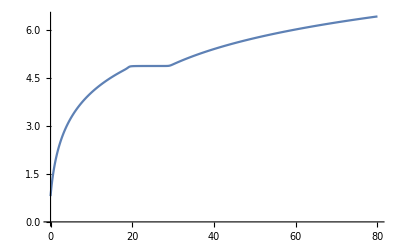

```mathematica
ListPlot[Table[{data[[i,1]],data[[i,2]]},{i,1,ndata}],Joined->True,PlotRange->All]
```

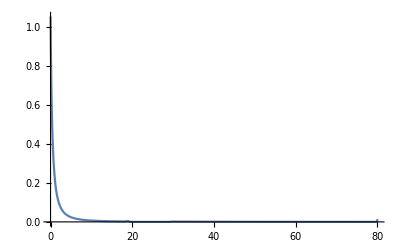

```mathematica
ListPlot[Table[{data[[i,1]],data[[i,3]]},{i,1,ndata}],Joined->True,PlotRange->All]
```

```mathematica
inputfile=OpenRead["Ps.txt"]
```

InputStream[…]

```mathematica
data=ReadList[inputfile,{Number,Number}];
```

```mathematica
Close[inputfile]
```

Ps.txt

```mathematica
ndata=Length[data]
```

1000

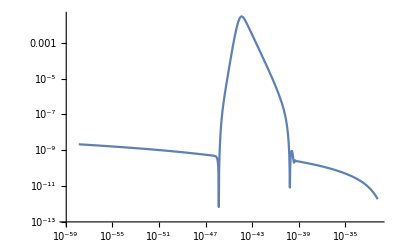

```mathematica
ListLogLogPlot[Table[{data[[i,1]],data[[i,2]]},{i,1,ndata}],Joined->True,PlotRange->All]
```

```mathematica
inputfile=OpenRead["fPBH.txt"]
```

InputStream[…]

```mathematica
data=ReadList[inputfile,{Number,Number}];
```

```mathematica
Close[inputfile]
```

fPBH.txt

```mathematica
ndata=Length[data]
```

1009

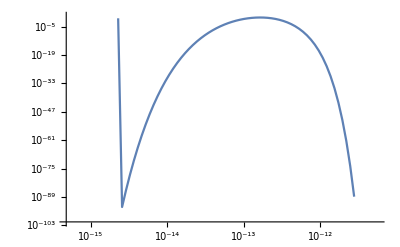

```mathematica
ListLogLogPlot[Table[{data[[i,1]],data[[i,2]]},{i,1,ndata}],Joined->True,PlotRange->All]
```

```mathematica
kpeak
```

```mathematica
Mpeak
```

```mathematica
fpeak
```

```mathematica
Pspeak
```

```mathematica
[10^5-10^4,10^5+10^4]
```

```mathematica
[0.044-0.001,0.044+0.001]
```

```mathematica
[0.9,1,1.1]
```